```mathematica
bfiles={Import["~/jennaproject/data/alpha_b2_0.0_br_0.001.txt","Table"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.002.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.003.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.004.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.005.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.006.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.007.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.008.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.009.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.010.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.011.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.012.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.013.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.014.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.015.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.016.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.017.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.018.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.019.txt","Data"],Import["~/jennaproject/data/alpha_b2_0.0_br_0.020.txt","Data"]};
```

```mathematica
Dimensions[bfiles]
```

{20,11,3}

```mathematica
bpts=Mean[bfiles[[#,All,1]]]&/@Range[1,Dimensions[bfiles][[1]]]
```

{1.0082,1.00803,1.00787,1.00771,1.00755,1.0074,1.00725,1.0071,1.00696,1.00682,1.00669,1.00655,1.00642,1.0063,1.00618,1.00606,1.00594,1.00583,1.00571,1.00561}

```mathematica
bvals=Range[0.001,0.02,0.001]
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02}

```mathematica
Dimensions[bvals]
```

{20}

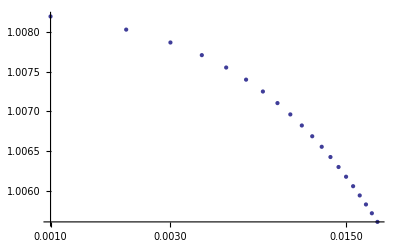

```mathematica
ListLogLinearPlot[{bvals,bpts}ᵀ]
```